# Non classical light and quadratures

```mathematica
<<Wolfram`QuantumFramework`
```

```mathematica
setFockSize[nmax_]:=Block[{},fockBasis =QuantumBasis[nmax];a=QuantumOperator[DiagonalMatrix[Table[Sqrt[i],{i,nmax-1}],1],nmax];
numberOp =a["Dagger"]@ a;
coherentTrunc =  QuantumState[Table[α^i/√(i!),{i,0,nmax-1}],nmax,"Parameters"->α];
coh = coherentTrunc["Normalize"];]
```

```mathematica
conmutator[a_QuantumOperator,b_QuantumOperator]:=a@b - b@a 
operatorVariance[state_QuantumState, op_QuantumOperator]:= (state["Dagger"]@ (op @ op)@ state)["Scalar"] - (state["Dagger"]@ op @ state)["Scalar"]^2
```

## Quadrature operators for a single field mode

```mathematica
setFockSize[40]
```

```mathematica
X1 = 1/2(a+a["Dagger"]);
```

```mathematica
X2 = 1/(2I)(a-a["Dagger"]);
```

[ X_1, X_2] = ⅈ/2 ,   but there is an error in the last term because of truncation

```mathematica
conmutator[X1,X2]
```

QuantumOperator[…]

```mathematica
With[{fockstates = fockBasis["BasisStates"]},Table[{operatorVariance[ fockstates[[i]],X1],operatorVariance[ fockstates[[i]],X2]},{i,1,10}]]
```

{{1/4,1/4},{3/4,3/4},{5/4,5/4},{7/4,7/4},{9/4,9/4},{11/4,11/4},{13/4,13/4},{15/4,15/4},{17/4,17/4},{19/4,19/4}}

For a fock state (Δ(X̂)_1()^2)_n=(Δ(X̂)_2()^2)_n = 1/4(2n+1), the ground state |0⟩ attains the minimum value  1/4

A coherent state is also a quantum state that minimizes the uncertainty of the quadrature operators (value of 1/4)

```mathematica
αc = 3.Exp[ⅈ RandomReal[{0,2π}]]
```

2.70685-1.29343 ⅈ

```mathematica
operatorVariance[coh[αc],X1]//Chop
```

0.25

```mathematica
operatorVariance[coh[αc],X2]//Chop
```

0.25

Also for a coherent state with a complex α it holds ⟨X_1⟩_α = Re(α)  and ⟨X_2⟩_α = Im(α)

```mathematica
(QuantumMeasurementOperator[N[#]]@ coh[αc])["Mean"]& /@ {X1,X2}
```

{2.70685,-1.29343}

Phase space picture its a circle with center (Re(α), Im(α)):

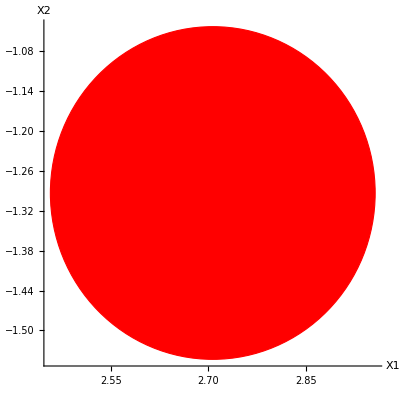

```mathematica
Graphics[{EdgeForm[Dashed],Directive[Red],Background->LightBlue,Disk[{Re[αc],Im[αc]},{operatorVariance[coh[αc],X1]//Chop,operatorVariance[coh[αc],X2]//Chop}]},Axes->True,AxesOrigin->{0,0},AxesLabel->(Style[#,14]&/@{"X1","X2"})]
```

### Squeezed operator

The unitary squeezed operator is defined as S(ξ) = exp(1/2 ξ^*a^2-1/2 ξ a^(†2))

```mathematica
squeeze[ξ_?NumericQ]:= Exp[1/2 Conjugate[ξ](a@a)-1/2ξ (a["Dagger"]@a["Dagger"])]
```

```mathematica
ξ1 = RandomReal[{0,0.8}]Exp[I RandomReal[{0,2π}]]
```

0.466944-0.229764 ⅈ

(S(ξ))^† = S(-ξ) = S^-1(ξ)

```mathematica
squeeze[ξ1]["UnitaryQ"]
((squeeze[ξ1]@squeeze[-ξ1])==QuantumOperator["I"[fockBasis["Dimension"]]])(* Identity operator*)
```

True

True

The properties S^†(ξ)a S(ξ)= a cosh r - a^†e^ⅈθ sinh r   and  S^†(ξ)a^† S(ξ)= a^† cosh r - ae^-ⅈθ sinh r
do not hold exactly because they rely on the commutator [a, a^†] = 1 that is not exact in a truncated Fock space

```mathematica
setFockSize[100]; squeeze[ξ_?NumericQ]:= Exp[1/2 Conjugate[ξ](a@a)-1/2ξ (a["Dagger"]@a["Dagger"])]
```

```mathematica
(squeeze[ξ1]["Dagger"]@ a @ squeeze[ξ1]);
```

```mathematica
With[{r = Abs[ξ1],θ = Arg[ξ1]},a Cosh[r]-a["Dagger"]Exp[I θ] Sinh[r]];
```

```mathematica
((% - %% )["Matrix"])//Abs //Chop//ArrayPlot
```

-Graphics-

### Squeezed coherent state: expectations

A squeezed coherent state is obtained applying the squeeze operator to a coherent state
|ξ, α⟩ = S(ξ)|α⟩ = S(ξ) D(α) |0⟩

```mathematica
setFockSize[120]; squeeze[ξ_?NumericQ]:= Exp[1/2 Conjugate[ξ](a@a)-1/2ξ (a["Dagger"]@a["Dagger"])]
```

```mathematica
{αcoh,ξ1} = RandomReal[{0,2},2]Exp[I RandomReal[{0,2π},2]]
```

{-0.366444+0.370297 ⅈ,-0.952915+0.527807 ⅈ}

```mathematica
squeezeCoh = squeeze[ξ1]@ coh[αcoh];
```

⟨ a ⟩ = α cosh(r) - α^* e^ⅈθ sinh(r)

```mathematica
(squeezeCoh["Dagger"]@N[a]@ squeezeCoh)["Scalar"]
```

-3.02808+3.40391 ⅈ

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},αcoh Cosh[r]-Conjugate[αcoh]Exp[I θ] Sinh[r]]
```

-3.04559+3.42607 ⅈ

```mathematica
(*(QuantumMeasurementOperator[N[a]]@ squeezeCoh)["Mean"]  QMO can work with non hermitian operators but only if the mean is real
, for this state is complex so it does not work *)
```

⟨ a^2 ⟩ = α^2 cosh^2(r) + (α^*)^2 e^(2ⅈθ)sinh^2(r)-2|(α|)^2 e^ⅈθ sinh(r)cosh(r)-e^ⅈθ cosh(r)sinh(r)

```mathematica
(squeezeCoh["Dagger"]@N[a@a]@ squeezeCoh)["Scalar"]
```

-3.3764-25.3607 ⅈ

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},αcoh^2 Cosh[r]^2+(αcoh*)^2 Exp[2 ⅈ θ] Sinh[r]^2-2 Abs[αcoh]^2 Exp[ⅈ θ]Sinh[r]Cosh[r]-Exp[I θ]Cosh[r]Sinh[r]]
```

-3.4946-25.9416 ⅈ

⟨ a^† a⟩ = |α|^2(cosh^2(r)+sinh^2(r))-(α*)^2 e^(ⅈ θ)sinh(r)cosh(r)-(α)^2 e^(- ⅈ θ)sinh(r)cosh(r) + sinh^2(r)

```mathematica
(* the number operator is an observable QMO works *)
```

```mathematica
(QuantumMeasurementOperator[numberOp]@squeezeCoh)["Mean"]
```

25.6455

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},Abs[αcoh]^2(Cosh[r]^2+Sinh[r]^2)+Sinh[r]^2-2Re[(αcoh^2 Exp[-I θ])]Cosh[r]Sinh[r]]//Re
```

25.7144

### Squeezed vacuum state: quadratures

Squeezed vacuum state  |ξ ⟩ = S(ξ) | 0 ⟩

```mathematica
squeezevacuum = squeeze[ξ1][];
```

```mathematica
Clear[X1,X2]
X1 = 1/2(a+a["Dagger"]);
X2 = 1/(2I)(a-a["Dagger"]);
```

The squeeze operator does not change the expectations of X1 and X2

```mathematica
(squeezevacuum["Dagger"]@N[X1]@ squeezevacuum)["Scalar"] //Chop
```

0

```mathematica
(squeezevacuum["Dagger"]@N[X2]@ squeezevacuum)["Scalar"] //Chop
```

0

```mathematica
operatorVariance[squeezevacuum,X1]//Chop
```

2.08431

```mathematica
operatorVariance[squeezevacuum,X2]//Chop
```

3.11648

Its known theoretically that  ⟨Δ X_1⟩^2 = 1/4 [ (cosh(r))^2+(sinh(r))^2-2sinh(r)cosh(r)cos(θ)]
and  ⟨Δ X_2⟩^2 = 1/4 [ (cosh(r))^2+(sinh(r))^2+2sinh(r)cosh(r)cos(θ)]

```mathematica
With[{r=Abs[ξ1],θ = Arg[ξ1]},Table[1/4(Cosh[r]^2+Sinh[r]^2-(-1)^m 2Sinh[r]Cosh[r]Cos[θ]),{m,0,1}]]
```

{2.08429,3.11652}

When θ = 0 the expressions reduce to  ⟨Δ X_1⟩^2 = 1/4 e^(-2r)    ⟨Δ X_2⟩^2 = 1/4 e^(2r)
For this case its clearly seen one quadrature gets “squeezed” while the other increases so it maintains the uncertainty principle, also in this case (θ = 0)  the inequality is saturated ( the product of uncertainties equals 1/16 = 0.0625). This is different from a coherent state or Fock state that also saturate the inequality, but they had the same value for the uncertainties in X_1 and X_2.

```mathematica
ξ1 = RandomReal[{0,1.5}]
squeezevacuum = squeeze[ξ1][];
```

1.32539

```mathematica
(operatorVariance[squeezevacuum,#]//Chop)& /@ {X1,X2}
```

{0.0815619,0.766289}

```mathematica
1/4{Exp[-2ξ1],Exp[2ξ1]}
```

{0.0815619,0.766289}

```mathematica
Times @@ %%
```

Phase space representation for the cases with θ = 0 and θ=π (not to scale for visual purposes), in these cases the squeezing is along the axes of X_1 or X_2 describing error ellipses

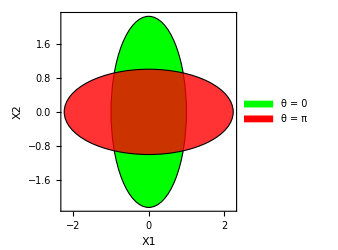

```mathematica
With[{dx =1, dy =operatorVariance[squeezevacuum,X2]/operatorVariance[squeezevacuum,X1]//Log}, Legended[Graphics[{EdgeForm[Dashed],Green,Disk[{0,0},{dx,dy}],Opacity[0.8],Red,Disk[{0,0},{dy,dx}]},Axes->True,Frame->True,ImageSize->250,AxesLabel->{"X1","X2"}],SwatchLegend[{Green,Red},{"θ = 0", "θ = π"}]]]
```

For a general  ξ = r e^ⅈθ we can defined rotated quadrature operators  Y_1 = cos(θ/2)X_1+ sin(θ/2)X_2  and Y_2= -sin(θ/2)X_1+cos(θ/2)X_2
such that the variances are calculated along the rotated quadrature axes. Because of that reason the value of the variances are  ⟨Δ Y_1 ⟩^2 = 1/4 e^(-2r)    ⟨Δ Y_2 ⟩^2 = 1/4 e^(2r) .  At  θ = 0   Y_1 and Y_2 reduce to X_1 and X_2

```mathematica
Y1 = QuantumOperator[Cos[θ/2]X1+Sin[θ/2]X2,"Parameters"->θ];
Y2 = QuantumOperator[-Sin[θ/2]X1+Cos[θ/2]X2,"Parameters"->θ];
```

```mathematica
{Y1[0] == X1, Y2[0] == X2}
```

{True,True}

```mathematica
ξ1 = RandomReal[{0,1.}] Exp[I RandomReal[{0,2Pi}]]
```

-0.217681-0.323297 ⅈ

```mathematica
squeezevacuum = squeeze[ξ1][];
```

```mathematica
With[{r = Abs[ξ1], θ1 = Arg[ξ1]}, operatorVariance[squeezevacuum,#]& /@ {Y1[θ1],Y2[θ1]}]//Chop
```

{0.163156,0.383069}

```mathematica
1/4{Exp[-2r],Exp[2r]}/. r->Abs[ξ1]
```

{0.163156,0.383069}

Phase space picture are rotated ellipses with angle of rotation θ/2  (the dashed lines represent the Y1 and Y2 quadrature axes)

```mathematica
Module[{θ1=Arg[ξ1],dx =1,dy}, 
dy =operatorVariance[squeezevacuum,Y2[θ1]]/operatorVariance[squeezevacuum,Y1[θ1]] ;Graphics[{EdgeForm[Thick],Green,
Rotate[Disk[{0,0},{dx,dy}],θ1/2],
Black,Dashed,Line[Outer[Times,{-dx,dx},{Cos[θ1/2],Sin[θ1/2]}]],Line[Outer[Times,{-dy,dy},{-Sin[θ1/2],Cos[θ1/2]}]
]},
Axes->True,Frame->True,ImageSize->Medium,AxesLabel->{"X1","X2"}]
]
```

-Graphics-

Visualization of the ellipse errors , the product of the variances of X_1 and X_2 only equals the uncertainty limit(1/16)  when the ellipses are alligned with the X_1 and X_2 axes

```mathematica
Manipulate[Module[{dx =1/4 Exp[-2r],dy =1/4Exp[2r]}, 
Graphics[{EdgeForm[Thick],Green,
Rotate[Disk[{0,0},{dx,dy}],θ1/2],
Black,Dashed,Line[Outer[Times,{-dx,dx},{Cos[θ1/2],Sin[θ1/2]}]],Line[Outer[Times,{-dy,dy},{-Sin[θ1/2],Cos[θ1/2]}]],Text[Framed[(ΔX1)^2 == 1/4(Cosh[r]^2+Sinh[r]^2-2Sinh[r]Cosh[r]Cos[θ1]),FrameStyle->Directive[Red,Thick,Dashing[0,0,0]]],{0.8,0.85}],Text[Framed[(ΔX2)^2 == 1/4(Cosh[r]^2+Sinh[r]^2+2Sinh[r]Cosh[r]Cos[θ1]),FrameStyle->Directive[Red,Thick,Dashing[0,0,0]]],{0.8,0.55}],Text[Framed[(ΔX1)^2(ΔX2)^2 == 1/16((Cosh[r]^2+Sinh[r]^2)^2-(2Sinh[r]Cosh[r]Cos[θ1])^2),FrameStyle->Directive[Red,Thick,Dashing[0,0,0]]],{0.75,-0.75}]
},
Axes->True,ImageSize->Medium,AxesLabel->{"X1","X2"},PlotRange->{{-1,1},{-1,1}},PlotLabel->"Quadratures of a squeezed vacuum state |ξ⟩"]]
,{{r,0,"Modulus r"},0,1},{{θ1,0,"Argument θ"},0,2π}]
```

For a squeezed vacuum state the photon statistics only has non zero values for even number of photons

```mathematica
ξ2 = RandomReal[{1,2}]Exp[ⅈ RandomReal[{0,2Pi}]];
```

```mathematica
(QuantumMeasurementOperator[numberOp]@ squeeze[ξ2][])["Probability"][[1;;10]];
```

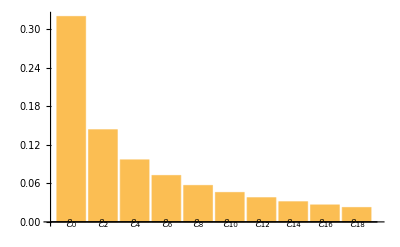

```mathematica
BarChart[%,ChartLabels->Keys[%]]
```

### Displaced squeezed state

A displaced squeezed state is defined as: |α, ξ ⟩ =  D(α) S(ξ) |0⟩, is not the same as a squeezed coherent state because the displacement operator and the squeeze operator do not commute

```mathematica
disp[x_?NumericQ] := Exp[x a["Dagger"]-Conjugate[x] a]
```

```mathematica
αcoh = 2Exp[I RandomReal[{0,2Pi}]]
```

1.28263+1.53456 ⅈ

Clearly the commutator is not 0

```mathematica
Take[conmutator[disp[αcoh],squeeze[ξ1]]["Amplitude"],10]
```

<|00→-0.152948+0.273499 ⅈ,01→-0.227312+0.375405 ⅈ,02→-0.0676402+0.295673 ⅈ,03→0.223293+0.112334 ⅈ,04→0.322641-0.0945065 ⅈ,05→0.0934831-0.243371 ⅈ,06→-0.222946-0.203328 ⅈ,07→-0.288821+0.0491472 ⅈ,08→-0.049079+0.27395 ⅈ,09→0.226611+0.19262 ⅈ|>

⟨a⟩ = α  , 		⟨a^2 ⟩ = α^2-e^(ⅈ θ)sinh(r)cosh(r) , 	⟨ a^†a ⟩= |α|^2+(sinh(r))^2
When r → 0, the results for a coherent state are recovered

```mathematica
dispSqueezed = disp[αcoh]@ squeeze[ξ1][];
```

```mathematica
{(dispSqueezed["Dagger"]@ a @ dispSqueezed)["Scalar"], αcoh}
```

{1.28263+1.53456 ⅈ,1.28263+1.53456 ⅈ}

```mathematica
With[{r = Abs[ξ1],θ1 = Arg[ξ1]},{(dispSqueezed["Dagger"]@ (a@a) @ dispSqueezed)["Scalar"],αcoh^2-ⅇ^(ⅈ θ1)Sinh[r]Cosh[r]}]
```

{-0.46932+4.29358 ⅈ,-0.46932+4.29358 ⅈ}

```mathematica
{(QuantumMeasurementOperator[numberOp]@ dispSqueezed)["Mean"],Abs[αcoh]^2 +Sinh[Abs[ξ1]]^2}
```

{4.15976,4.15976}

For this state it still holds  ⟨Δ Y_1 ⟩^2 = 1/4 e^(-2r)    ⟨Δ Y_2 ⟩^2 = 1/4 e^(2r)
That can be interpreted that the error ellipses keep their shape for any ξ, but the center is displaced by α

```mathematica
With[{r = Abs[ξ1], θ1 = Arg[ξ1]}, {operatorVariance[dispSqueezed,#]& /@ {Y1[θ1],Y2[θ1]}//Chop,1/4{Exp[-2r],Exp[2r]}}]
```

{{0.114659,0.545097},{0.114659,0.545097}}

```mathematica
ξ1 = RandomReal[{0.4,0.7}]Exp[I RandomReal[{0,2Pi}]];αcoh = RandomReal[{1.2,1.5}]Exp[I RandomReal[{0,2Pi}]];
```

```mathematica
Module[{θ1=Arg[ξ1],dx ,dy, h=Re[αcoh], k = Im[αcoh]}, 
dx = operatorVariance[dispSqueezed,Y1[θ1]];dy =operatorVariance[dispSqueezed,Y2[θ1]] ;Graphics[{EdgeForm[Thick],Green,
Rotate[Disk[{h,k},{dx,dy}],θ1/2],
Black,Dashed,Line[#+{h,k}&/@Outer[Times,{-dx,dx},{Cos[θ1/2],Sin[θ1/2]}]],Line[#+{h,k}& /@ Outer[Times,{-dy,dy},{-Sin[θ1/2],Cos[θ1/2]}]
],PointSize[0.022],Point[{h,k}],{Red,Dashing[1,0,0],Arrow[{{0,0},{h,k}}],Text["α",{0.05*h,0}+{h,k}/2]}},
Axes->True,Frame->True,ImageSize->Medium,AxesLabel->{"X1","X2"}]
]
```

-Graphics-

## Homodyne detection

```mathematica
setFockSize[40]
```

```mathematica
a1 = QuantumTensorProduct[a,QuantumOperator["I"[fockBasis["Dimension"]]]];
a2 = QuantumTensorProduct[QuantumOperator["I"[fockBasis["Dimension"]]],a];
```

```mathematica
st = QuantumState["25",fockBasis];
(st["Dagger"]@ (a1["Dagger"]@a1)@ st)["Scalar"]
(st["Dagger"]@ (a2["Dagger"]@a2)@ st)["Scalar"]
```

2

5

Using a balanced BS it can be proved :   i_34= n_3-n_4=a_3^†a_3-a_4^†a_4=-2[1/(2 ⅈ)(a_2^†a_1-a_1^†a_2)]
n_3-n_4 is related to the photocurrent difference which is an observable with direct experimental interpretation

```mathematica
i34 = -1/ⅈ(a2["Dagger"]@a1-a1["Dagger"]@a2);
```

Given an input state which β being a coherent state and ψ any state : |in⟩ = (|ψ⟩)_1(|β⟩)_2       ⟨n_3-n_4⟩ =  ⟨i_34⟩ = 2 |β | ⟨ X(ϕ+π/2) |ψ⟩
where ϕ is the phase of the complex β. We can define θ = ϕ + π/2 and quadrature at angle θ is defined X(θ) = 1/2(a e^(-ⅈ θ)+ a^†e^(ⅈ θ)), to vary θ we vary ϕ and get different quadrature measurements	. For the variances of the quadratures we get a similar formula
 ⟨(Δ(i_34))^2⟩ = 4 |β |^2 ⟨(Δ( X(θ)))^2⟩

We try also  with a coherent state in the signal port, but has to be weaker than the local oscillator strong coherent field

```mathematica
ψ = coh[0.5+0.72I];
```

```mathematica
osciAmp = 3;
```

```mathematica
cohOsci = QuantumState[coh[osciAmp Exp[I θ]]];
```

```mathematica
in = QuantumState[QuantumTensorProduct[ψ,cohOsci],"Parameters"->θ];
```

```mathematica
quadratures = Table[(in[x]["Dagger"]@i34 @ in[x])["Scalar"]//Chop,{x,N@Subdivide[0,2Pi,40]}];
```

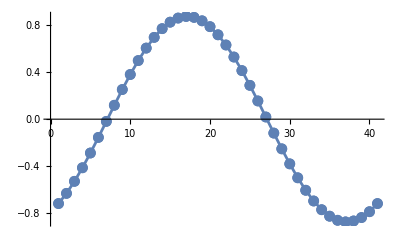

```mathematica
ListLinePlot[{quadratures/6},Mesh->Full]
```

For a coherent state we can extract the parameters easily

```mathematica
{Abs[0.5+0.72I],Max[quadratures]/(2 osciAmp)}
```

{0.876584,0.876385}

```mathematica
quadratures[[{1,1+Quotient[Length@quadratures,4]}]]/(2 osciAmp)
```

{-0.72,0.5}

```mathematica
ξ1 = 0.15 Exp[ⅈ RandomReal[{0,2π}]]
```

-0.0769251-0.128773 ⅈ

```mathematica
Xtheta[θ_?NumericQ]:= 1/2(a Exp[-ⅈ θ]+a["Dagger"]Exp[ⅈ θ])
```

For a squeezed vacuum the expectation of the quadratures is zero

```mathematica
ψ = squeeze[ξ1][];
```

```mathematica
in = QuantumState[QuantumTensorProduct[ψ,cohOsci],"Parameters"->θ];
```

```mathematica
quadratures = Table[(in[x]["Dagger"]@i34 @ in[x])["Scalar"]//Chop,{x,N@Subdivide[0,2Pi,40]}];
```

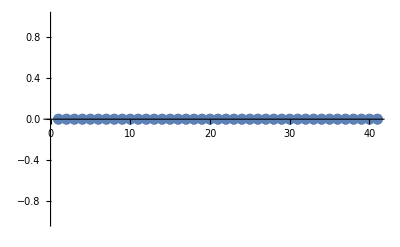

```mathematica
ListLinePlot[{quadratures/6},Mesh->Full]
```

But not the variances

```mathematica
ψ = squeeze[ξ1] @coh[0.5+0.72I];
```

```mathematica
in = QuantumState[QuantumTensorProduct[ψ,cohOsci],"Parameters"->θ];
```

```mathematica
quadratures = Table[(in[x]["Dagger"]@i34 @ in[x])["Scalar"]//Chop,{x,N@Subdivide[0,2Pi,40]}];
```

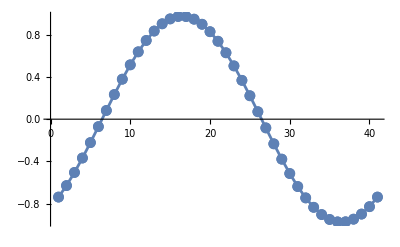

```mathematica
ListLinePlot[{quadratures/(2 osciAmp)},Mesh->Full]
```

```mathematica
quadratures2 = Table[(ψ["Dagger"]@Xtheta[x-Pi/2] @ ψ)["Scalar"]//Chop,{x,N@Subdivide[0,2Pi,40]}];
```

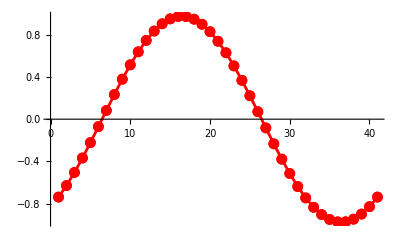

```mathematica
ListLinePlot[quadratures2,Mesh->Full,PlotStyle->Red]
```

```mathematica
variances = Table[operatorVariance[in[x],N[i34]]//Chop,{x,N@Subdivide[0,2Pi,40]}];
```

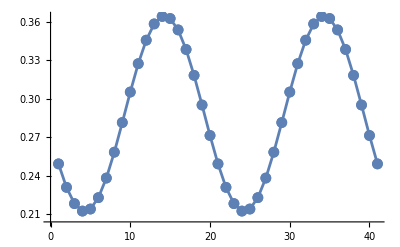

```mathematica
ListLinePlot[variances / (4 osciAmp^2),Mesh->Full]
```

```mathematica
variances2 = Table[operatorVariance[ψ,Xtheta[x-Pi/2]]//Chop,{x,N@Subdivide[0,2Pi,40]}];
```

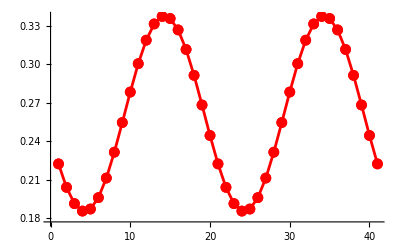

```mathematica
ListLinePlot[variances2,Mesh->Full,PlotStyle->Red]
```